```mathematica
f[x_,y_]=Cos[3Pi/8(x-y)]Sin[2Pi (x+y)/3]Exp[x/4-y/7]
```

ⅇ^(x/4-y/7) sin(2/3 π (x+y)) cos(3/8 π (x-y))

```mathematica
{ax,bx}={-1,1}; {ay,by}={-1,1};
```

```mathematica
gradF[x_,y_]={D[f[x,y],x],D[f[x,y],y]}//FullSimplify
```

{1/24 ⅇ^(x/4-y/7) (2 cos(3/8 π (x-y)) (3 sin(2/3 π (x+y))+8 π cos(2/3 π (x+y)))-9 π sin(3/8 π (x-y)) sin(2/3 π (x+y))),1/168 ⅇ^(x/4-y/7) (63 π sin(3/8 π (x-y)) sin(2/3 π (x+y))+8 cos(3/8 π (x-y)) (14 π cos(2/3 π (x+y))-3 sin(2/3 π (x+y))))}

```mathematica
Plot3D[f[x,y],{x,ax,bx},{y,ay,by},PlotTheme->"ZMesh",AxesLabel->{"x", "y","z"}]
```

-Graphics3D-

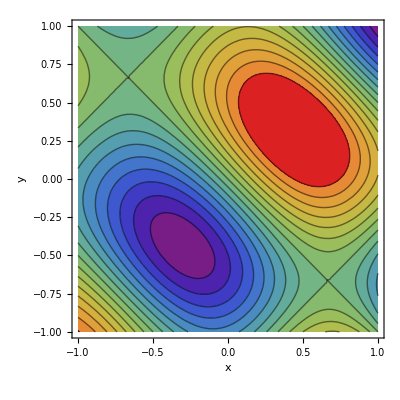

```mathematica
cp=ContourPlot[f[x,y],{x,ax,bx},{y,ay,by},ContourShading->Automatic,Contours->16,FrameLabel->{"x","y"}]
```

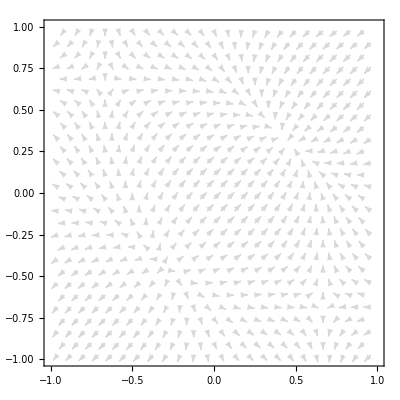

```mathematica
vp=VectorPlot[gradF[x,y],{x,ax,bx},{y,ay,by},VectorScaling->"Log",VectorColorFunction->Function[{x,y},LightGray],VectorPoints->24,VectorMarkers->Placed["Arrow","Start"],VectorSizes->Small]
```

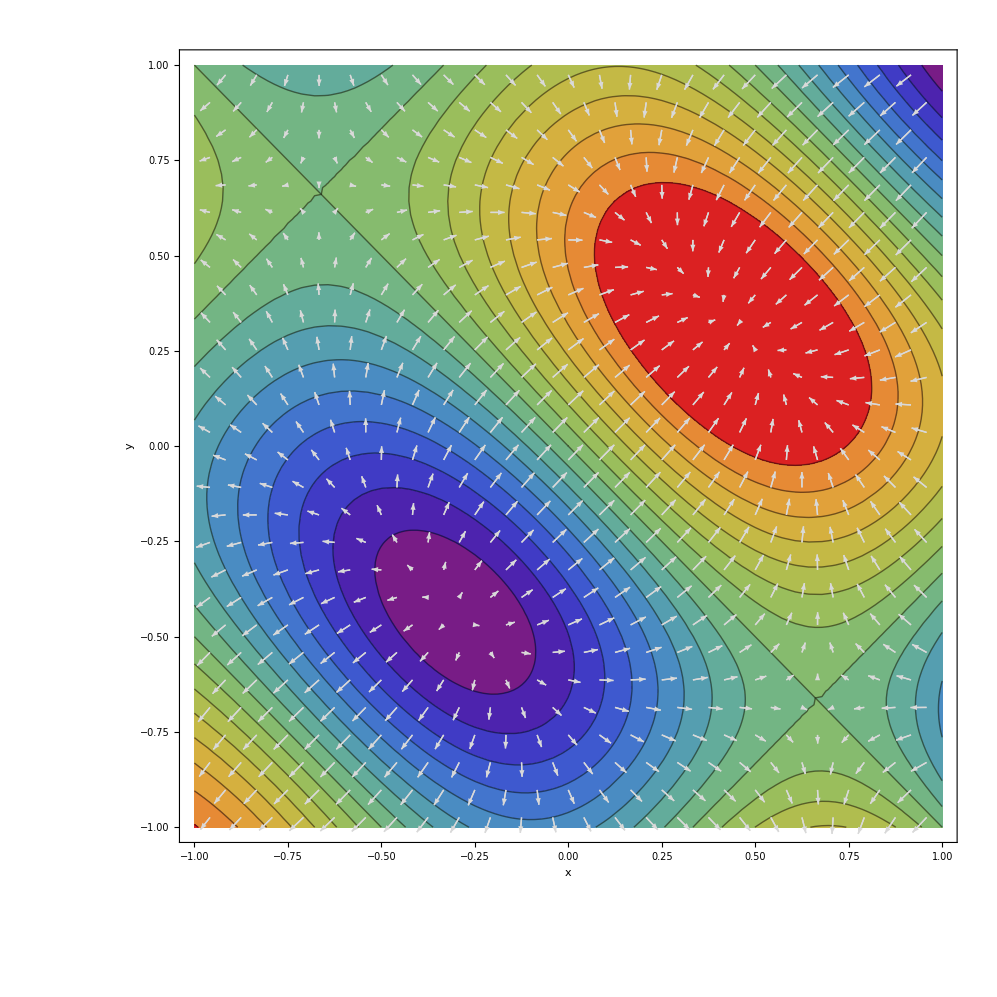

```mathematica
xp=Show[cp,vp]
```